# 弹簧与微分方程

```mathematica
NDSolve[{-k x[t]-u x'[t]==m x''[t],x[0]==3,x'[0]==0}/.{k->10,u->2,m->5},{x,x'},{t,0,15}]
```

{{x→InterpolatingFunction[…],x'→InterpolatingFunction[…]}}

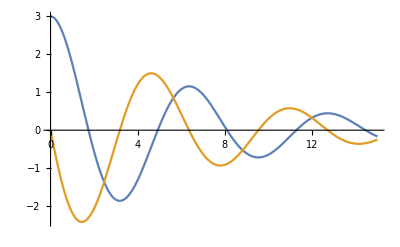

```mathematica
{pos,vel}=NDSolveValue[{-k x[t]-u x'[t]==m x''[t],x[0]==3,x'[0]==0}/.{k->10,u->3,m->10},{x,x'},{t,0,15}];
Plot[{pos[t],vel[t]},{t,0,15},PlotRange->All]
```

### 2维，有初速度

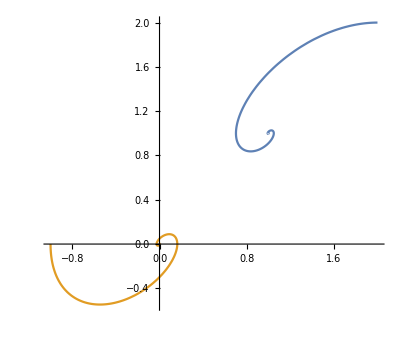

```mathematica
{pos,vel}=NDSolveValue[{k ({1,1}-x[t])-u x'[t]==m x''[t],x[0]=={2,2},x'[0]=={-1,0}}/.{k->10,u->10,m->10},{x,x'},{t,0,15}];
ParametricPlot[{pos[t],vel[t]},{t,0,15},PlotRange->All]
```

### 上面其实更像万有引力

### 水平面上一个长度为1、劲度系数为k的弹簧，一端固定在原点，另一端连接一个质量为m的小球，设置小球的初始位置和速度，计算其位置和速度随时间的变化

只考虑随速度变化的阻力

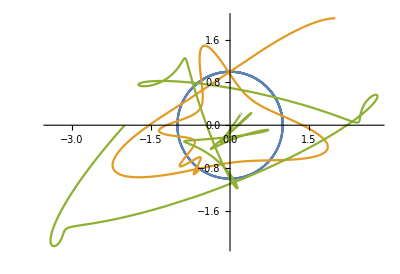

```mathematica
{pos,vel}=NDSolveValue[{k (Normalize[x[t]]-x[t])-u x'[t]==m x''[t],x[0]=={2,2},x'[0]=={-2,0}}/.{k->50,u->3,m->10},{x,x'},{t,0,15}];
ParametricPlot[{{Cos[t],Sin[t]},pos[t],vel[t]},{t,0,15},PlotRange->All]
```

```mathematica
pos
```

InterpolatingFunction[…]

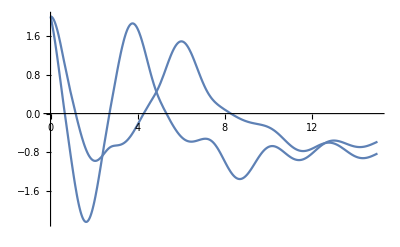

```mathematica
Plot[%28[x],{x,0.,15.}]
```

## 可视化

画一个弹簧

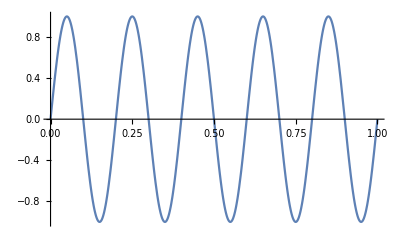

```mathematica
Plot[Sin[2 π 5 x],{x,0,1}]
```

将弹簧两端固定到任意两个点

```mathematica
DynamicModule[{pts=RandomPoint[Disk[{0,0},3],2],v},LocatorPane[Dynamic[pts],Dynamic@Show[v=Complex@@(pts[[2]]-pts[[1]]);ParametricPlot[RotationMatrix[Arg[v]].{Abs[v]x,Sin[2 π 5 x]}+pts[[1]],{x,0,1},PlotRange->3],Graphics[{Magenta,PointSize[Large],Point[pts]}]]]]
```

```mathematica
DynamicModule[{pt1={0,0},pt2={2,2},v},LocatorPane[Dynamic[pt2,{pt2=#&,{pos,vel}=NDSolveValue[{k (Normalize[x[t]]-x[t])-u x'[t]==m x''[t],x[0]==#,x'[0]=={-2,0}}/.{k->50,u->3,m->10},{x,x'},{t,0,15}]&}],Dynamic[v=Complex@@(pt2-pt1);
Show[ParametricPlot[{{Cos[t],Sin[t]},pos[t],vel[t]},{t,0,15},PlotRange->All],ParametricPlot[RotationMatrix[Arg[v]].{Abs[v]x,Sin[2 π 5 x]}+pt1,{x,0,1},PlotRange->3],Graphics[{Magenta,PointSize[Large],Point[pt2]}],ImageSize->Large]]]]
```

Set::shape: 列表 {pos,vel} 和 NDSolveValue[{k Plus[«2»]-Times[«2»]==m x''[t],x[0]==#1,x'[0]=={-2,0}}/.{k→50,u→3,m→10},{x,x'},{t,0,15}]& 形状不同.